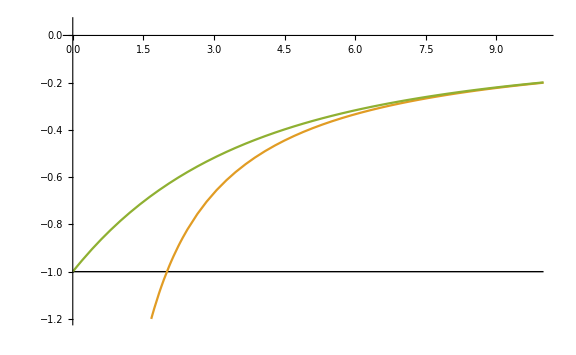
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 1

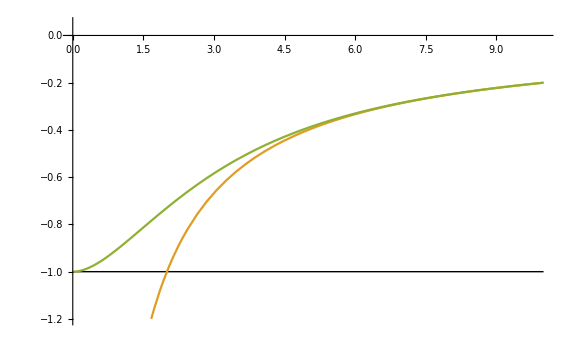
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 2

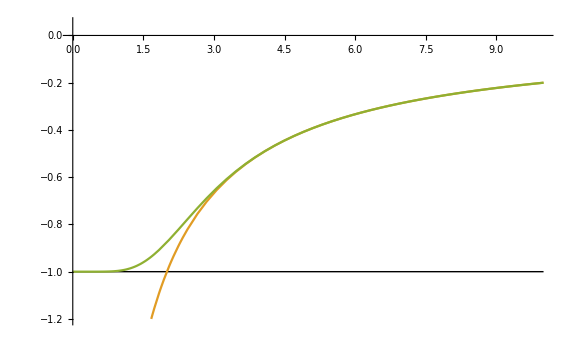
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 10

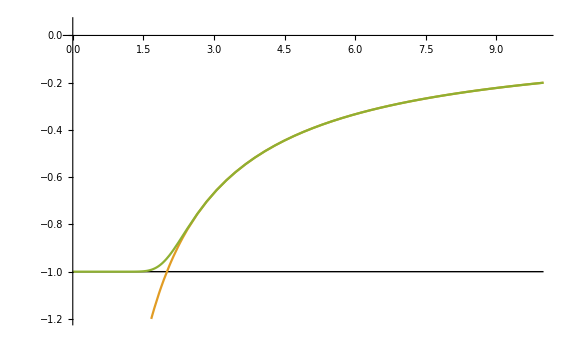
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 50

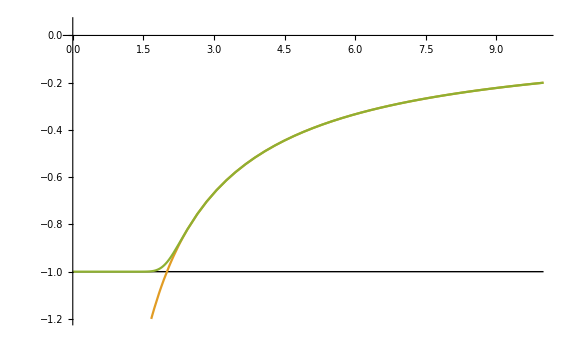
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 100

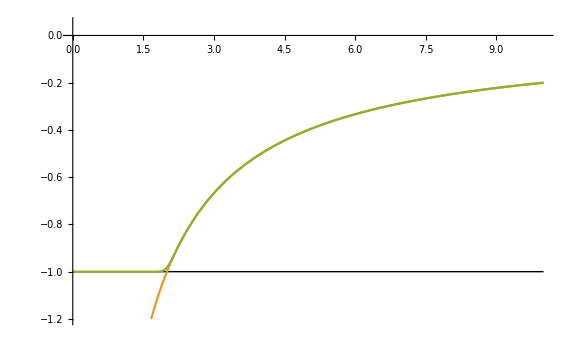
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 500

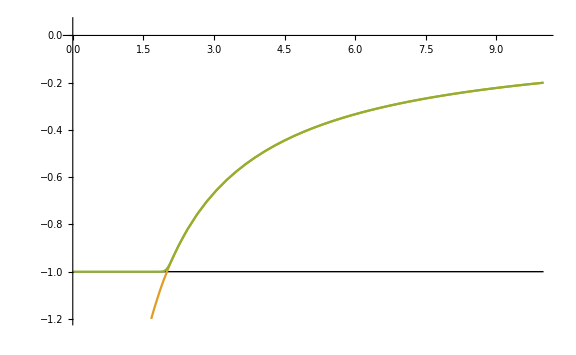
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 1000

```mathematica
Block[{g,prec},
prec=240;
g[𝒩_,α_]:=-2/r+Exp[-α r]Sum[(α r)^(n-1)/(n!)(2α-n),{n,0,𝒩}];
plt[xp_]:=Plot[
{Style[-1,DotDashed],-2/r,xp},{r,0,10},
PlotRange->{-1.2,0.05},
WorkingPrecision->prec,PerformanceGoal->"Quality",ImageSize->Large
];
Off[General::munfl];
Do[
gexp=g[𝒩,𝒩/2];
Labeled[plt[gexp],{r/(u Subscript[r, AU]),"E/(u SubscriptBox[E, AU])","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
Print[];
,{𝒩,{1,2,10,50,100,500,1000}}
];
On[General::munfl];
]
```

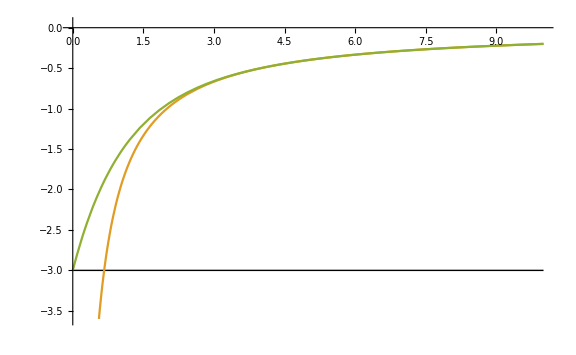
-Graphics-r/r_AUE/E_AU𝒩 = 1

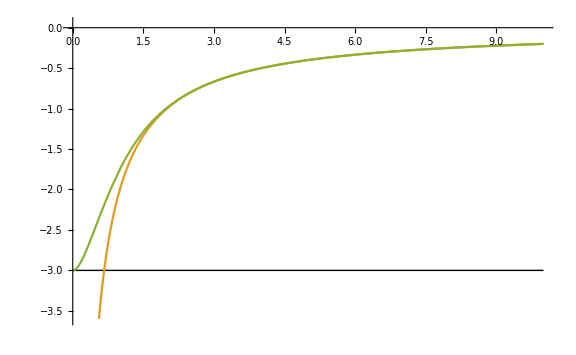
-Graphics-r/r_AUE/E_AU𝒩 = 2

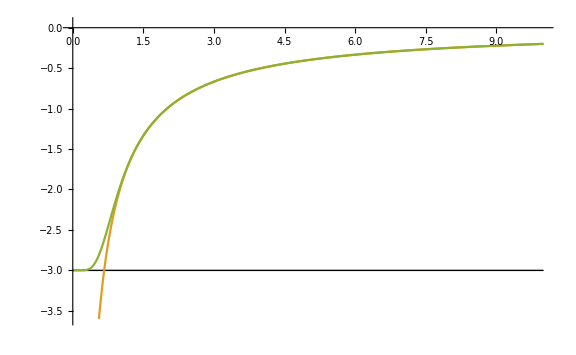
-Graphics-r/r_AUE/E_AU𝒩 = 10

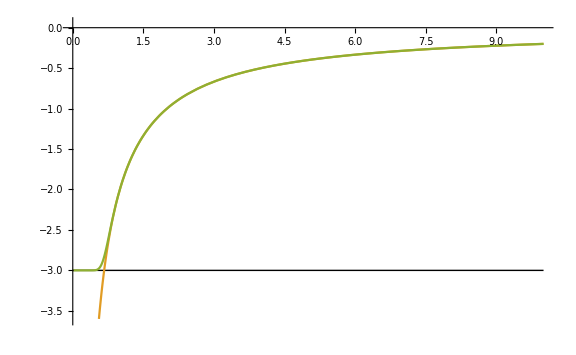
-Graphics-r/r_AUE/E_AU𝒩 = 50

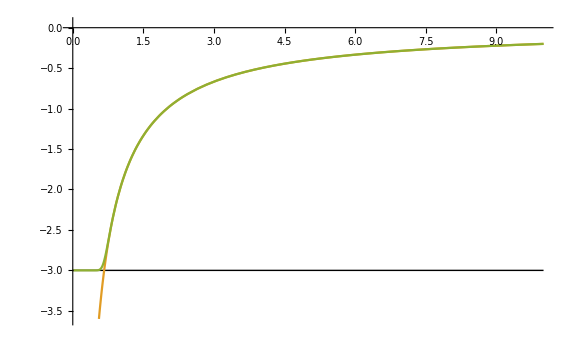
-Graphics-r/r_AUE/E_AU𝒩 = 100

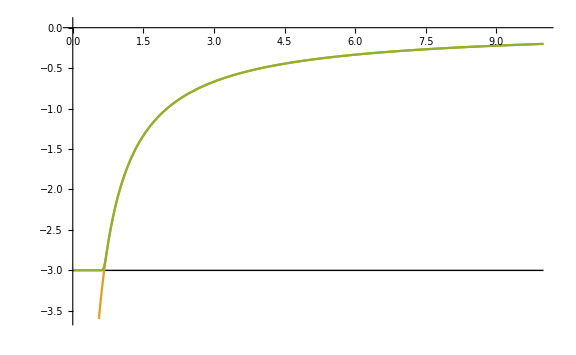
-Graphics-r/r_AUE/E_AU𝒩 = 500

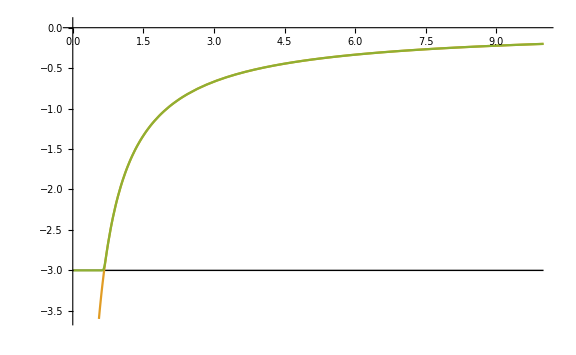
-Graphics-r/r_AUE/E_AU𝒩 = 1000

```mathematica
Block[{g,U0,prec},
g[r_,𝒩_,α_]:=-2/r(1-Exp[-α r]/(2α)Sum[(α r)^n/(n!)(2α-n),{n,0,𝒩}]);
U0=3;prec=240;
plt[xp_]:=Plot[
{Style[-U0,DotDashed],-2/r,xp},{r,0,10},
PlotRange->{-1.2*U0,0.05},
WorkingPrecision->prec,PerformanceGoal->"Quality",ImageSize->Large
];
Off[General::munfl];
Do[
gexp=U0 g[U0 r,𝒩,𝒩/2];
Labeled[plt[gexp],{r/Subscript[r, AU],"E/E_AU","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
Print[];
,{𝒩,{1,2,10,50,100,500,1000}}
];
On[General::munfl];
]
```

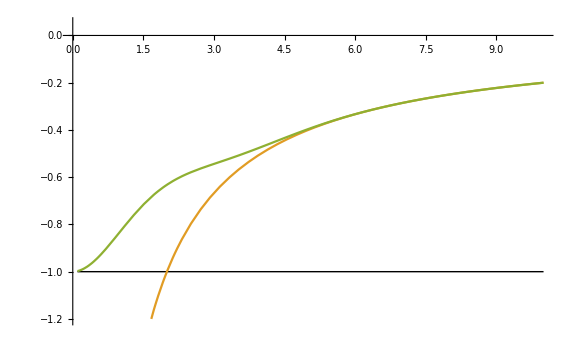
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 1

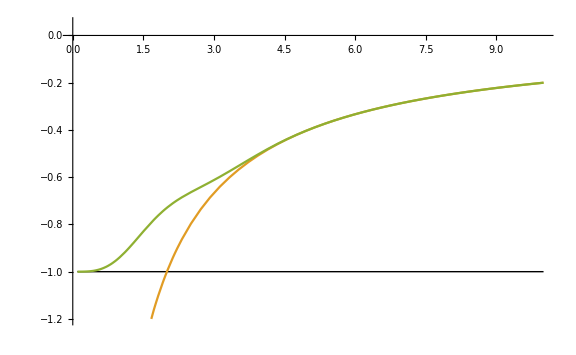
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 2

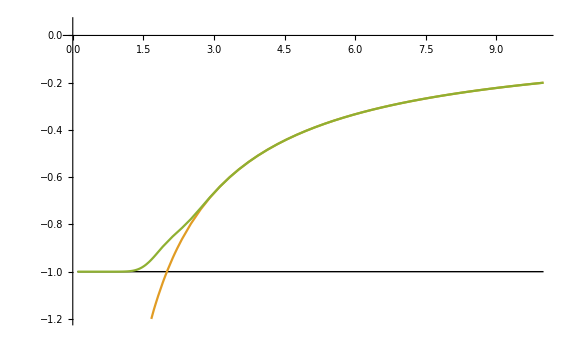
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 10

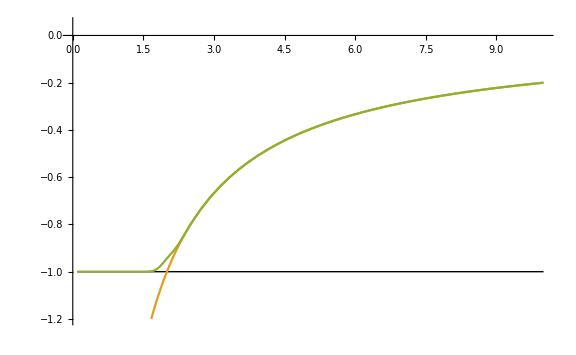
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 50

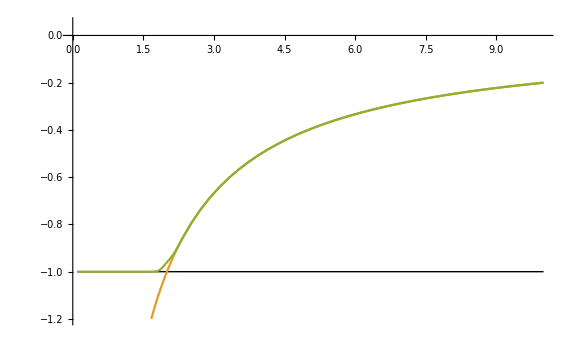
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 100

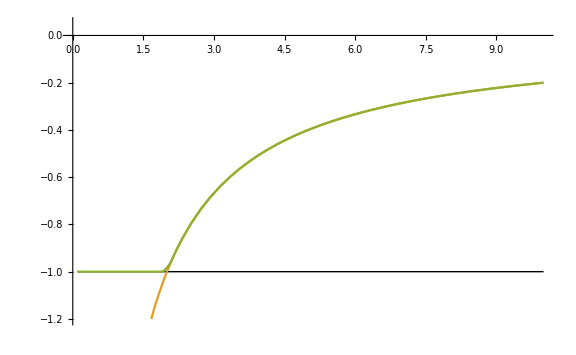
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 500

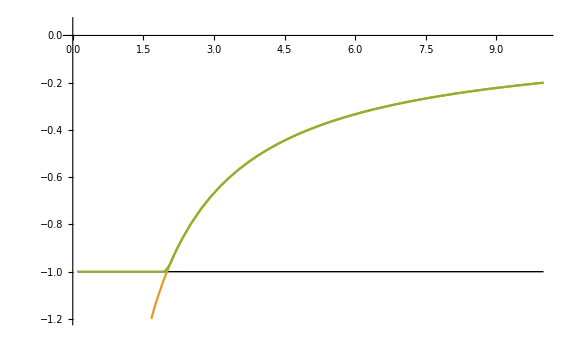
-Graphics-r/(u r_AU)E/(u SubscriptBox[E, AU])𝒩 = 1000

```mathematica
Block[{prec,f,g},
prec=240;
f[𝒩_,ℬ_]:=(1-r/2)(Sum[(ℬ r)^(2n)/(n!),{n,0,𝒩-1}])+(ℬ r)^(2𝒩)/(𝒩!);
g[𝒩_,ℬ_]:=-2/r(1-Exp[-(ℬ r)^2]f[𝒩,ℬ]);
plt[xp_]:=Plot[
{Style[-1,DotDashed],-2/r,xp},{r,0.1,10},
PlotRange->{-1.2,0.05},
WorkingPrecision->prec,PerformanceGoal->"Quality",ImageSize->Large
];
Off[General::munfl];
Do[
gexp=SetPrecision[g[𝒩,(√𝒩)/2],prec];
Labeled[plt[gexp],{r/(u Subscript[r, AU]),"E/(u SubscriptBox[E, AU])","𝒩 = "<>ToString[𝒩]},{Top,Left,Bottom}]//Print;
Print[];
,{𝒩,{1,2,10,50,100,500,1000}}
];
On[General::munfl];
]
```